The Geometry of Lagrange Multipliers

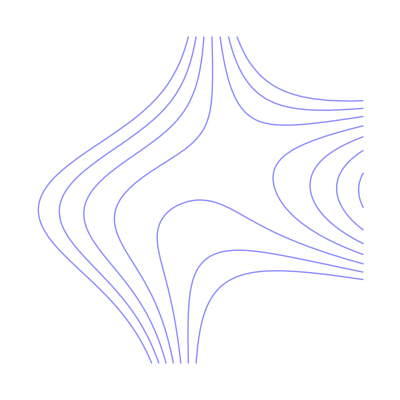
```mathematica
Manipulate[
Pane[Column[{
Dynamic[Refresh[Pane[Text@Column[{TraditionalForm[Row[{Style["f",Italic],"(",Style["x",Italic],",",Style["y",Italic],") = ",f@@p0}]], ExtrLabel[p0]}],ImageSize->{Automatic,28},Alignment->Top],TrackedSymbols:>{p0}]],
If[threeD,
Show[constraint3d,fn3d,Graphics3D[With[{P=Append[p0,f@@p0],z0=f@@p0},{Black,PointSize[Medium],Point[P],Lighter[Blue],MyArrow[{P,Append[p0+∇f/.Thread[{x,y}->p0],z0]}],ColorData["SolarColors"][0.3],MyArrow[{P,Append[p0+∇g/.Thread[{x,y}->p0],z0]}],ColorData["SolarColors"][0.6],MyArrow[{P,Append[p0+(∇f/.Thread[{x,y}->p0]).#/#.# #&@Cross[∇g/.Thread[{x,y}->p0]],z0]}]}]],
PlotRange->{{-5,5},{-5,5},{-9,12}},BoxRatios->{1,1,0.8},ViewPoint->Dynamic[vp],ViewVertical->Dynamic[vv],SphericalRegion->True,ImageSize->$MyImageSize],
LocatorPane[Dynamic[p0,(p0=If[#=={0.,0.},$p0,t0#/.Quiet[FindRoot[g@@(t0 #)==1/4,{t0,2/Norm[#]}]],$p0])&],Show[fn2d,constraint2d,PlotRange->5,ImageSize->$MyImageSize],Appearance->{Dynamic[Graphics[{Black,PointSize[Medium],Tooltip[Point[{0,0}],f@@p0],Lighter[Blue],Arrow[{{0,0},∇f/.Thread[{x,y}->p0]}],ColorData["SolarColors"][0.3],Arrow[{{0,0},∇g/.Thread[{x,y}->p0]}],ColorData["SolarColors"][0.6],Arrow[{{0,0},(∇f/.Thread[{x,y}->p0]).#/#.# #&@Cross[∇g/.Thread[{x,y}->p0]]}]},PlotRange->5,ImageSize->$MyImageSize]]},Exclusions->{{0.,0.}}]
]}],ImageSize->{5+$MyImageSize,30+$MyImageSize},Alignment->Center],
{{threeD,True,"show"},{True->"3D",False->"2D"},SetterBar},
{{p0,{1.3160740129524926,0},"point"},Dynamic[LocatorPane[Dynamic[p0,(p0=If[#=={0.,0.},{1.3160740129524926,0},rg[#]{Cos[#],Sin[#]}&[ArcTan@@#],{1.3160740129524926,0}])&],Show[fn2d,constraint2d,PlotRange->5,ImageSize->120],Exclusions->{{0.,0.}}],SynchronousUpdating->False]&},
{{vp,{1.3,-2.4,2}},None},
{{vv,{0,0,1}},None},
AutorunSequencing->{1},
ControlPlacement->Left,TrackedSymbols:>{p0,threeD},
SynchronousInitialization->False,
Initialization:>(
$MyImageSize={400,400};
Del[fn_]:=D[fn[x,y],{{x,y}}];
g[x_,y_]:=((x^2+y^2)^2-12 x y)/12;
rg[θ_]:=Sqrt[3 Sin[2θ]+Sqrt[9 Sin[2θ]^2+3]]; (* g == 1/4 in polar *)
f[x_,y_]:=(x^2-x y^2+3 y)/2;
MyArrow[{p1_,p2_}]:=If[p1≠p2,Module[{x,v},v=(p2-p1)*(1-0.3/Norm[p2-p1]);x=Cross[Normalize[p2-p1],{0,0,1}];
{Thick,EdgeForm[],Line[{p1,p1+v}],Polygon[{p2,p1+v+0.12x,p1+v-0.12x}]
}],{}];
fn2d=-Graphics-;
constraint2d=
-Graphics-;
fn3d=-Graphics3D-;
constraint3d=-Graphics3D-;
extrema=Sort[{x,y}//.{Reduce[{∇f.Cross[∇g]==0,g[x,y]==1/4},{x,y},Reals]//N//ToRules},ArcTan@@#1<ArcTan@@#2&];
ExtrLabel[p0_]:=Function[i,Style[Row[{"near ",If[EvenQ[i],"min","max"]}],12,GrayLevel[1-E^(-20(p0-extrema⟦i⟧).(p0-extrema⟦i⟧))]]][Ordering[extrema,1,Norm[p0-#1]<Norm[p0-#2]&]⟦1⟧];
)]
```

Move a point around a constraint curve to see the relationship between the blue gradient of the function f(x,y) to be optimized and the red gradient of the function g(x,y) for the constraint g(x,y)=0. The orange vector is the projection of the gradient of f onto the tangent line of the constraint curve; its direction is the direction of increase along the constraint and its magnitude is the slope (that is, the directional derivative) of f in that direction. There are both 2D and 3D views, with the constraint curve laid out upon the graph of the function.

At a local extremum, the gradients of the functions f and g are parallel. Thus we get the condition for an extremum ∇f = λ ∇g, where λ is called a Lagrange multiplier.

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

constrained

extrema

optimization

Lagrange multiplier

multivariable calculus

Lagrange Multiplier

Contributed by: Michael Rogers (Oxford College of Emory University)